```mathematica
Interpolation for Scatterer Potential
```

```mathematica
xe={{6.486,0.976},{6.569,0.612},{6.63,0.234},{6.675,0.008},{6.736,-0.177},{6.811,-0.352},{6.902,-0.526},{6.992,-0.664},{7.113,-0.791},{7.28,-0.886},{7.431,-0.914},{7.567,-0.909},{7.718,-0.881},{7.914,-0.829},{8.111,-0.758},{8.322,-0.682},{8.489,-0.621},{8.67,-0.56},{8.912,-0.484},{9.214,-0.404},{9.441,-0.347},{9.652,-0.309},{9.856,-0.276}}
```

(6.486 | 0.976
6.569 | 0.612
6.63 | 0.234
6.675 | 0.008
6.736 | -0.177
6.811 | -0.352
6.902 | -0.526
6.992 | -0.664
7.113 | -0.791
7.28 | -0.886
7.431 | -0.914
7.567 | -0.909
7.718 | -0.881
7.914 | -0.829
8.111 | -0.758
8.322 | -0.682
8.489 | -0.621
8.67 | -0.56
8.912 | -0.484
9.214 | -0.404
9.441 | -0.347
9.652 | -0.309
9.856 | -0.276)

```mathematica
funct=Interpolation[xe]
```

InterpolatingFunction[{{6.486, 9.856}}, <>]

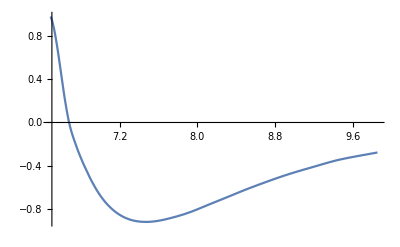

```mathematica
Plot[funct[x],{x,6.486,9.856}]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
NonlinearModelFit[xe,{a/x^12-b/x^6},{a,b},x]
```

FittedModel[(2.94085×10^10)/x^12-325882./x^6]

```mathematica
%22["BestFit"]
```

(2.94085×10^10)/x^12-325882./x^6

```mathematica
Plot[%23,{x,3,20}]
```